```mathematica
ex = {1,0, 0};
ey = {0,1, 0};
ez = {0, 0, 1};
r10 = {-dx, 0, 0};
r20 = {dx, 0, 0};

θ1 = y1[t];
θ2 = y2[t];
x = y3[t];

ω1 = D[θ1, t];
ω2 = D[θ2, t];
v = D[x,t];

α1 = D[ω1, t];
α2 = D[ω2, t];
a = D[v,t];

r1 = r10 + l {Sin[θ1], -Cos[θ1], 0};
r2 = r20 + l {Sin[θ2], -Cos[θ2], 0};


v0 = {v, 0, 0};
v1 = v0 + (ω1 ez)×(r1 - r10)
v2 = v0 + (ω2 ez)×(r2 - r20)

PE = m g (Dot[r1,ey] + Dot[r2,ey])
KE = 1/2 M Dot[v0,v0] + 1/2 m Dot[v1,v1] + 1/2 m Dot[v2,v2]
L = Simplify[KE-PE]
(*Lalt = Simplify[1/2(M+2 m)v^2 + m v l (Cos[θ1]ω1 + Cos[θ2]ω2) + 1/2 m l^2(ω1^2+ω2^2) + m g l(Cos[θ1] + Cos[θ2])];
Simplify[L - Lalt]*)
```

{l Cos[y1[t]] y1'[t]+y3'[t],l Sin[y1[t]] y1'[t],0}

{l Cos[y2[t]] y2'[t]+y3'[t],l Sin[y2[t]] y2'[t],0}

g m (-l Cos[y1[t]]-l Cos[y2[t]])

1/2 M y3'[t]^2+1/2 m (l^2 Sin[y1[t]]^2 y1'[t]^2+(l Cos[y1[t]] y1'[t]+y3'[t])^2)+1/2 m (l^2 Sin[y2[t]]^2 y2'[t]^2+(l Cos[y2[t]] y2'[t]+y3'[t])^2)

1/2 (2 g l m Cos[y1[t]]+2 g l m Cos[y2[t]]+l^2 m y1'[t]^2+l^2 m y2'[t]^2+2 l m Cos[y1[t]] y1'[t] y3'[t]+2 l m Cos[y2[t]] y2'[t] y3'[t]+2 m y3'[t]^2+M y3'[t]^2)

```mathematica
Simplify[D[D[L,ω1],t]/.{y1->"θ1", y2->"θ2", y3->"x"}]
Simplify[D[L,θ1]/.{y1->"θ1", y2->"θ2", y3->"x"}]
```

l m (-Sin[θ1[t]] x'[t] θ1'[t]+Cos[θ1[t]] x''[t]+l θ1''[t])

-l m Sin[θ1[t]] (g+x'[t] θ1'[t])

```mathematica
repr = {y1->"θ1", y2->"θ2", y3->"x"};
eq1 = Simplify[(D[D[L,ω1],t] ==  D[L,θ1])];
eq2 = Simplify[(D[D[L,ω2],t] ==  D[L,θ2])]; 
eq3 = Simplify[(D[D[L,v],t] == D[L, x])];
eq1/.repr
eq2/.repr
eq3/.repr
```

l m (g Sin[θ1[t]]+Cos[θ1[t]] x''[t]+l θ1''[t])==0

l m (g Sin[θ2[t]]+Cos[θ2[t]] x''[t]+l θ2''[t])==0

(2 m+M) x''[t]+l m Cos[θ1[t]] θ1''[t]+l m Cos[θ2[t]] θ2''[t]==l m (Sin[θ1[t]] θ1'[t]^2+Sin[θ2[t]] θ2'[t]^2)

```mathematica
sol = Simplify[Solve[{eq1,eq2,eq3}, {y1''[t], y2''[t], y3''[t]}]]
```

{{y1''[t]→(g (3 m Sin[y1[t]]+2 M Sin[y1[t]]-m Sin[y1[t]-2 y2[t]])+l m Sin[2 y1[t]] y1'[t]^2+2 l m Cos[y1[t]] Sin[y2[t]] y2'[t]^2)/(l (-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]])),y2''[t]→(g (m Sin[2 y1[t]-y2[t]]+3 m Sin[y2[t]]+2 M Sin[y2[t]])+2 l m Cos[y2[t]] Sin[y1[t]] y1'[t]^2+l m Sin[2 y2[t]] y2'[t]^2)/(l (-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]])),y3''[t]→-(m (g (Sin[2 y1[t]]+Sin[2 y2[t]])+2 l Sin[y1[t]] y1'[t]^2+2 l Sin[y2[t]] y2'[t]^2))/(-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]])}}

```mathematica
deqn = {a - γv}/.sol[[1]]
deqn = Equal @@@ sol[[1]]
de
```

{y1''[t]==(g (3 m Sin[y1[t]]+2 M Sin[y1[t]]-m Sin[y1[t]-2 y2[t]])+l m Sin[2 y1[t]] y1'[t]^2+2 l m Cos[y1[t]] Sin[y2[t]] y2'[t]^2)/(l (-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]])),y2''[t]==(g (m Sin[2 y1[t]-y2[t]]+3 m Sin[y2[t]]+2 M Sin[y2[t]])+2 l m Cos[y2[t]] Sin[y1[t]] y1'[t]^2+l m Sin[2 y2[t]] y2'[t]^2)/(l (-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]])),y3''[t]==-(m (g (Sin[2 y1[t]]+Sin[2 y2[t]])+2 l Sin[y1[t]] y1'[t]^2+2 l Sin[y2[t]] y2'[t]^2))/(-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]])}

```mathematica
params={
m-> 0.050,
M-> 10.0,
g-> 9.8,
l -> 0.5
};
dinit ={
y1[0]==10 °, y2[0]==-14 °, y3[0]==0,
y1'[0]==2.0, y2'[0]==0, y3'[0]==0
};
dsol = NDSolve[Join[deqn /. params,dinit], {y1[t],y2[t],y3[t]},{t,0,1000}]
```

{{y1[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],y2[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],y3[t]→InterpolatingFunction[{{0., 1000.}}, <>][t]}}

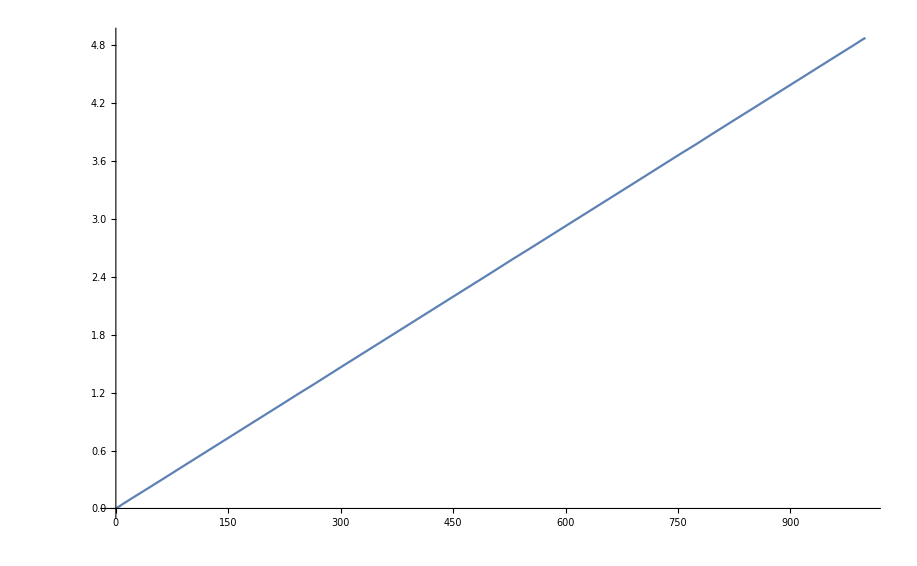

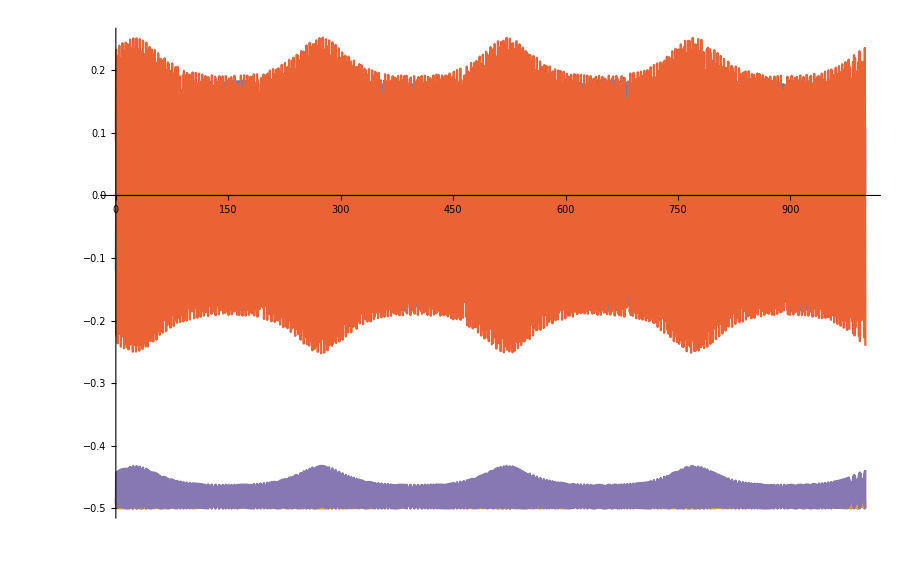

```mathematica
Plot[y3[t]/.params/.dsol, {t,0,1000}]
Plot[Evaluate[{r2-r20, r1-r10}/.params/.dsol], {t,0,1000}]
```